5.6454

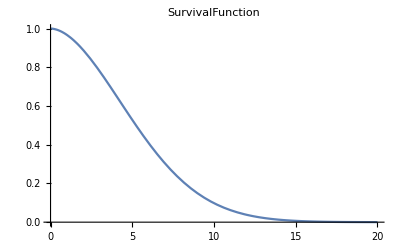
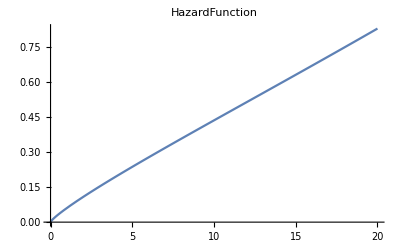
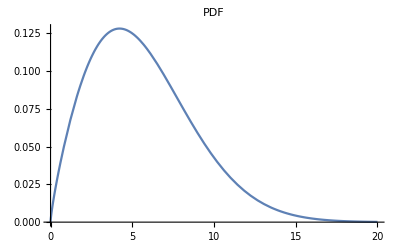
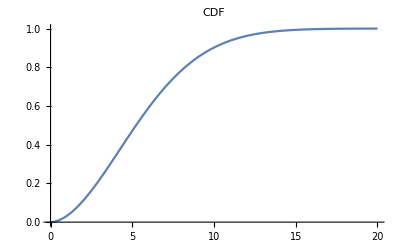

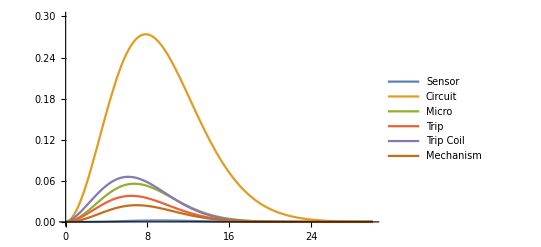

```mathematica
breakerVals1={a1->3.6,b1->29.7,a2->1.9,b2->8.9,a3->1.9,b3->17.9,a4->1.8,b4->23.1,a5->1.6,b5->19.7,a6->2.1,b6->23.7};ℛbreaker1=ReliabilityDistribution[sensor∧circuit∧micro∧trip∧actuator∧mechanism,{{sensor,WeibullDistribution[a1,b1]},{circuit,WeibullDistribution[a2,b2]},{micro,WeibullDistribution[a3,b3]}, {trip,WeibullDistribution[a4,b4]},{actuator,WeibullDistribution[a5,b5]},{mechanism,WeibullDistribution[a6,b6]}}];
mttf1=Mean[ℛbreaker1/.breakerVals1]
Table[Plot[df2[ℛbreaker1/.breakerVals1,t],{t,0,20},PlotLabel->df2,PlotRange->All],{df2,{SurvivalFunction,HazardFunction,PDF,CDF}}]
Plot[Evaluate@(ImprovementImportance[ℛbreaker1,t]/.breakerVals1),{t,0,30},PlotRange->{0,0.3},PlotLegends-> Placed[{"Sensor","Circuit","Micro","Trip","Trip Coil","Mechanism"},Right]]
(*Plot[Evaluate@(ImprovementImportance[ℛbreaker1,t]/.breakerVals1),{t,0,30},PlotStyle->{Dashing[{0.04,0.04}],Dotted,Automatic},PlotRange->{0,0.3},PlotLegends-> Placed[{"sensor","circuit","micro","trip","actuator","mechanism"},Right]]*)
```

```mathematica
ℛbreaker2=ReliabilityDistribution[sensor∧circuit∧micro∧trip∧(actuator1∨actuator2)∧mechanism,{{sensor,WeibullDistribution[a1,b1]},{circuit,WeibullDistribution[a2,b2]},{micro,WeibullDistribution[a3,b3]}, {trip,WeibullDistribution[a4,b4]},{actuator1,WeibullDistribution[a51,b51]},{actuator2,WeibullDistribution[a52,b52]},{mechanism,WeibullDistribution[a6,b6]}}];
breakerVals2=Join[breakerVals1,{a51->1.6,b51->19.7,a52->1.6,b52->19.7}];
mttf2=Mean[ℛbreaker2/.breakerVals2]
(*Table[Plot[df2[ℛbreaker2/.breakerVals2,t],{t,0,20},PlotLabel->df2,PlotRange->All,Filling->Axis],{df2,{SurvivalFunction,HazardFunction,PDF,CDF}}]*)
```

6.09456

WeibullDistribution[1.30239,13.9029]

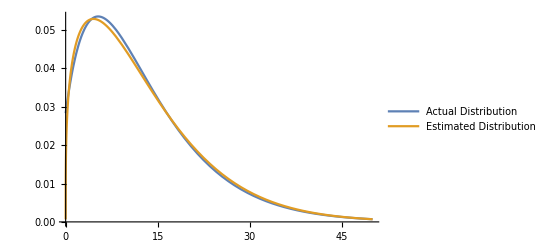

```mathematica
breakerVals3=breakerVals2;
𝒟Circuit=WeibullDistribution[a2,b2];
𝒟Micro=WeibullDistribution[a3,b3];
𝒟CircuitMicro=ReliabilityDistribution[x∧y,{{x,𝒟Circuit},{y,𝒟Micro}}];
SeedRandom[1120];
data𝒟CircuitMicro=RandomVariate[𝒟CircuitMicro/.breakerVals3,2000];
e𝒟CircuitMicro=EstimatedDistribution[data𝒟CircuitMicro,ExponentialDistribution[α]];
(*e𝒟CircuitMicro=EstimatedDistribution[data𝒟CircuitMicro,WeibullDistribution[α,β]]*)
𝒮SelfTest=StandbyDistribution[e𝒟CircuitMicro,{e𝒟CircuitMicro},0.8];
dataSelfTest=RandomVariate[𝒮SelfTest/.breakerVals3,2000];
e𝒟SelfTest=EstimatedDistribution[dataSelfTest,WeibullDistribution[α,β]]
Plot[{PDF[𝒮SelfTest/.breakerVals3,x],PDF[e𝒟SelfTest/.breakerVals3,x]},{x,0,50},PlotLegends->{"Actual Distribution","Estimated Distribution"}]
```

```mathematica
ℛbreaker3Self=ReliabilityDistribution[sensor∧circuitWithST∧trip∧(actuator1∨actuator2)∧mechanism,{{sensor,WeibullDistribution[a1,b1]},{circuitWithST,e𝒟SelfTest}, {trip,WeibullDistribution[a4,b4]},{actuator1,WeibullDistribution[a51,b51]},{actuator2,WeibullDistribution[a52,b52]},{mechanism,WeibullDistribution[a6,b6]}}];
ℛbreaker3ValuesSelf=ℛbreaker3Self/.breakerVals3;
mttf3=Mean[ℛbreaker3ValuesSelf]
(*Table[Plot[df2[ℛbreaker3Self/.breakerVals3,t],{t,0,20},PlotLabel->df2,PlotRange->All,Filling->Axis],{df2,{SurvivalFunction,HazardFunction,PDF,CDF}}]*)
```

8.08911

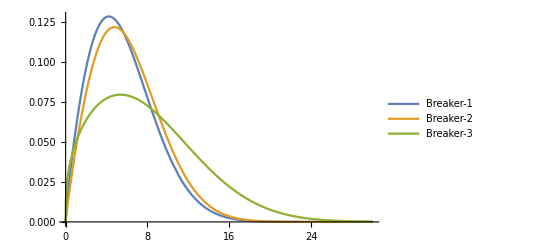

```mathematica
Plot[{PDF[ℛbreaker1/.breakerVals1,x],PDF[ℛbreaker2/.breakerVals2,x],PDF[ℛbreaker3Self/.breakerVals3,x]},{x,0,30},PlotLegends->{"Breaker-1","Breaker-2","Breaker-3"}]
```